```mathematica
Impedance[α0_,χ0_,U0_,θ0_,η0_,P0_]:=
Module[{α=α0,U=U0,P,rule,X,L,n,smoothingFunc,v,V,max,vacuum,plasma,u,hg,υ,ϵ,g,system,R,T,RP,Dissipation},
(*α - dissipation, α==ν/ω, ω->ω(1+ⅈα);
χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L==v'[Subscript[x, 0]]^-1 where v[Subscript[x, 0]]==0;
U - anizatropy: p^2==4πe^2*n/m, b==eB/(mc), v==p^2/ω^2, u==b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα);
θ - angel between wave vector and XOY;
η - angle between wave vector projection and density gradient direction;
P - wave polarisation in native mode (O-X); 2d-vector*)

(*=====================================================================================================================*)
(*Natural plasma parameters,without dimensionlesses*)
Subscript[X, 0]=3;Subscript[V, max]=2;(*plasma boundary and depth; it makes reflection point equal to -Subscript[X, 0] √(1-1/Subscript[V, max]) for U==0*)
n=0.1;(*smoothing width, in parts of plasma whight*)
υ=Function[x,Subscript[V, max](1-x^2/Subscript[X, 0]^2)(*(2 Subscript[V, max] √(1-1/Subscript[V, max])x/Subscript[X, 0])*)];smoothingFunc=Function[x,(1+(x/Subscript[X, 0])^(2/n))^-1];
v=Function[x,υ[x]smoothingFunc[x](1-ⅈ α)];u=U(1-ⅈ α);
(*=====================================================================================================================*)
L=υ'[hg/.NSolve[υ[hg]==1(*-U*)&&-Subscript[X, 0]<hg<0,hg]⟦1⟧]^-1;(*For dimensionless*)
ϵ=Function[x,1-v[x L]/(1-u)];Subscript[ϵ, l]=Function[x,1-v[x L]];g=Function[x,(√u)/(1-u)v[x L]];
(*=====================================================================================================================*)
rule={Subscript[$k, 0]->χ0/L,$θ->θ0,$η->η0,$u->u,$X->Subscript[X, 0]/L,$ϵ->ϵ,Subscript[$ϵ, l]->Subscript[ϵ, l],$g->g};
Subscript[T, vp]=If[η0==0,Subscript[Υ, vp^s],Subscript[Υ, vp^r]]/.rule;
Subscript[T, pv]=If[η0==0,Subscript[Υ, pv^s],Subscript[Υ, pv^r]]/.rule;
P=Subscript[T, vp].P0;(*vacuum polarisation*)
system={eq,ic}/.rule;
Subscript[R, vacuum]=(Subscript[$R, general]/.NDSolve[system,{tt[x],st[x],ts[x],ss[x]},{x,-2 Subscript[X, 0] /L,2 Subscript[X, 0]/ L}])⟦1⟧;
RP=Subscript[R, vacuum].P/.x->-2 Subscript[X, 0]/L;
Dissipation=1-(Abs[RP⟦1⟧]^2+Abs[RP⟦2⟧]^2)/(Abs[P⟦1⟧]^2+Abs[P⟦2⟧]^2);
Subscript[R, plasma]=Subscript[T, pv].Subscript[R, vacuum].Subscript[T, vp];
{Dissipation,Subscript[R, plasma],Subscript[R, vacuum],Subscript[T, vp],Subscript[T, pv],Subscript[X, 0]/ L}
];
```

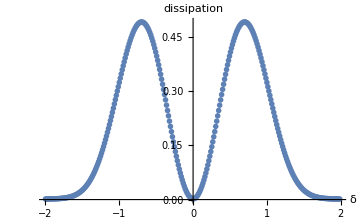

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/isotropism/isotropism.csv

```mathematica
(*Isotropic dimensionless dissipation for X-wave; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ]*)
δDissipation={};
χ=100;β=0;η=0;
δbegining=-2;δend=2;δnstep=300;
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δDissipation=Append[δDissipation,{δ,Impedance[10^-5,χ,(β*χ^(-2/3))^2,ArcSin[δ*χ^(-1/3)],η,{0,1}]⟦1⟧}];
];
ListPlot[δDissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"},ImageSize->Medium]
SaveData[config["isotropism","data"],δDissipation]
Clear[χ,β,δ,η,δbegining,δend,δnstep];
```

```mathematica
(*Anisotropic dimensionless dissipation for X-wave, η == 0; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ], β == χ^(2/3)√u*)
δβDissipation={};
χ=100;
δbegining=-2;δend=2;δnstep=100;
βbegining =0; βend = 1; βnstep = 100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)+((βend-βbegining)/βnstep)*(δ-δbegining)/(δend-δbegining)]]
For[β=βbegining,β<βend,β+=(βend-βbegining)/βnstep,
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δβDissipation=Append[δβDissipation,{δ,β,Impedance[10^-5,χ,(β*χ^(-2/3))^2,ArcSin[δ*χ^(-1/3)],0,{0,1}]⟦1⟧}];
];
];
ListPlot3D[δβDissipation,PlotRange->Full,AxesLabel->{"δ","β","dissipation"}]
SaveData[config["teta","data"],δβDissipation]
Clear[χ,δ,β,δβDissipation,δbegining,δend,δnstep,βbegining,βend,βnstep];
```

-Graphics3D-

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/teta.csv

```mathematica
(*Anisotropic dimensionless dissipation for O-wave, θ == 0; σ == (2 √2 Subscript[πχ, 0] u^(1/4))^(-1/2)*)
ηχDissipation={};
σ=0.07;
χbegining=(2 √2 π σ^2)^-1+1;χend=(2 √2 π σ^2)^(-3/2)-1;χnstep=10;ηnstep = 50;
ProgressIndicator[Dynamic[(χ-χbegining)/(χend-χbegining)]]
For[χ=χbegining,χ<χend,χ+=(χend-χbegining)/χnstep,
υ=(2 √2 π χ σ^2)^-4;H=ArcSin[√(√υ/(1+√υ))];ηbegining=H-3σ;ηend=H+3σ;
For[η=ηbegining,η<ηend,η+=(ηend-ηbegining)/ηnstep,
AppendTo[ηχDissipation,{(η-H)/σ,χ,Impedance[10^-5,χ,υ,0,η,{1,0}]⟦1⟧}];
];
];
ListPlot3D[ηχDissipation,PlotRange->Full,AxesLabel->{"δη/σ","χ","dissipation"}]
SaveData[config["eta","data"],ηχDissipation]
Clear[ηχDissipation,χ,σ,η,H,υ,χbegining,χend,χnstep,ηnstep,ηbegining,ηend,experiment,theory,result];
```

-Graphics3D-

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/eta.csv

```mathematica
(2 √2 π σ^2)^2/.σ->0.05//N
(2 √2 π υ^(1/4) σ^2)^-1/.υ->10^-6(2 √2 π σ^2)^2/.σ->0.05//N
(2 √2 π υ^(1/4) σ^2)^-1/.υ->10^-2.77/.σ->0.2//N
```

0.00049348

9550.97

13.8594

```mathematica
(*Anisotropic dimensionless dissipation for O-wave, θ == 0; σ == (2 √2 Subscript[πχ, 0] u^(1/4))^(-1/2)*)
σηυDissipation={};
σbegining=0.1;σend=0.11;σnstep=1;
ProgressIndicator[Dynamic[(σ-σbegining)/(σend-σbegining)]]
ProgressIndicator[Dynamic[Log[(υend/υbegining)^(1/υnstep),υ/υbegining]/υnstep]]
ProgressIndicator[Dynamic[(η-ηbegining)/(ηend-ηbegining)]]
For[σ=σbegining,σ<σend,σ+=(σend-σbegining)/σnstep,
ηυDissipation={};
υend=(2 √2 π σ^2)^2;υbegining=10^-4.5 υend;υnstep=50;ηnstep = 50;
For[υ=υbegining,υ≤υend,υ*=(υend/υbegining)^(1/υnstep),
υcr=(2 √2 π σ^2)^(4/3)υ^(1/3);ηcr=υcr^(1/4);
ηbegining=0;ηend=2ηcr;
For[η=ηbegining,η≤ηend,η+=(ηend-ηbegining)/ηnstep,
AppendTo[ηυDissipation,{η/ηcr,Log[10,υ/υcr],Impedance[10^-5,(2 √2 π υ^(1/4) σ^2)^-1,υ,0,η,{1,0}]⟦1⟧}];
];
];
SaveData[config["eta","directory"]<>"low-field-"<>ToString[σ]<>".csv",ηυDissipation];
AppendTo[σηυDissipation,{σ,ηυDissipation}];
];
Table[ListPointPlot3D[σηυDissipation⟦i,2⟧,PlotRange->Full,AxesLabel->{"η/η_cr","log_10(υ/υ_cr)","dissipation"},PlotLabel->ToString[σηυDissipation⟦i,1⟧],ImageSize->Medium],{i,1,Length[σηυDissipation]}]
(*SaveData[config["eta","low-field"],σηυDissipation]*)
Clear[ηυDissipation,σ,η,υ,υcr,ηcr,σbegining,σend,σnstep,υbegining,υend,υnstep,ηnstep,ηbegining,ηend,experiment,theory,result];
```

{-Graphics3D-}

{0.878402,{α→2.2264,ϕ→1.90496}}

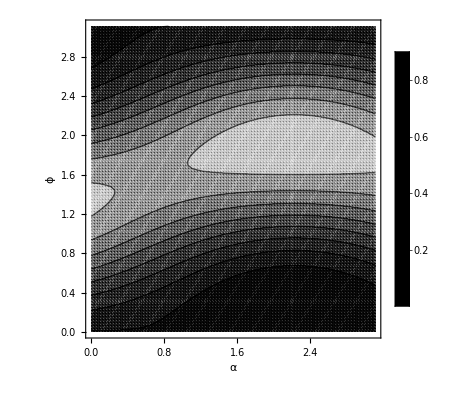

```mathematica
αϕDissipation={};
αbegining=0;αend=π;αnstep=100;
ϕbegining=0;ϕend=π;ϕnstep=100;
ProgressIndicator[Dynamic[(α-αbegining)/(αend-αbegining)]]
For[α=αbegining,α<αend,α+=(αend-αbegining)/αnstep,
For[ϕ=ϕbegining,ϕ<ϕend,ϕ+=(ϕend-ϕbegining)/ϕnstep,
P={Sin[ϕ],Cos[ϕ] ⅇ^(ⅈ α)};
SubPlus[V]=U.P;
SubMinus[V]=R.SubPlus[V];
AppendTo[αϕDissipation,{α,ϕ,1-(Abs[SubMinus[V]⟦1⟧]^2+Abs[SubMinus[V]⟦2⟧]^2)/(Abs[SubPlus[V]⟦1⟧]^2+Abs[SubPlus[V]⟦2⟧]^2)}];
];
];
Clear[α,ϕ,P,V];
NMaximize[{Interpolation[αϕDissipation][α,ϕ],αbegining<α<αend&&ϕbegining<ϕ<ϕend},{α,ϕ}]//Quiet
ListContourPlot[αϕDissipation,PlotRange->Full,FrameLabel->{"α","ϕ"},PlotLegends->Automatic,PlotTheme->"Monochrome"]
```

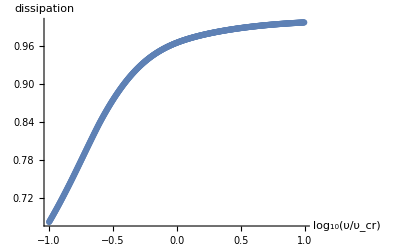

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/polarisation.csv

```mathematica
(*Anisotropic dimensionless dissipation for different polarisations, θ == 0; σ == (2 √2 Subscript[πχ, 0] u^(1/4))^(-1/2)*)
σ=0.08;
υPolarisation={};
υDissipation={};
υbegining=10^(-3/2)(2 √2 π σ^2)^2;υend=10^(3/2)(2 √2 π σ^2)^2;υnstep=500;
αbegining=0;αend=π;αnstep=100;
ϕbegining=0;ϕend=π;ϕnstep=100;
ProgressIndicator[Dynamic[Log[(υend/υbegining)^(1/υnstep),υ/υbegining]/υnstep]]
For[υ=υbegining,υ≤υend,υ*=(υend/υbegining)^(1/υnstep),
υcr=(2 √2 π σ^2)^(4/3)υ^(1/3);η =ArcSin[√((√υ)/(1+√υ))];ηcr=υcr^(1/4);
sol=Impedance[10^-5,(2 √2 π υ^(1/4) σ^2)^-1,υ,0,If[η/ηcr>0.7,η,0.7ηcr],{1,0}];
R=sol⟦3⟧/.x->-2sol⟦6⟧;
U=sol⟦4⟧;

αϕDissipation={};
For[α=αbegining,α<αend,α+=(αend-αbegining)/αnstep,
For[ϕ=ϕbegining,ϕ<ϕend,ϕ+=(ϕend-ϕbegining)/ϕnstep,
P={Sin[ϕ],Cos[ϕ] ⅇ^(ⅈ α)};
SubPlus[V]=U.P;
SubMinus[V]=R.SubPlus[V];
AppendTo[αϕDissipation,{α,ϕ,1-(Abs[SubMinus[V]⟦1⟧]^2+Abs[SubMinus[V]⟦2⟧]^2)/(Abs[SubPlus[V]⟦1⟧]^2+Abs[SubPlus[V]⟦2⟧]^2)}];
];
];
Clear[α,ϕ];
maxDiss=NMaximize[{Interpolation[αϕDissipation][α,ϕ],αbegining<α<αend&&ϕbegining<ϕ<ϕend},{α,ϕ}]//Quiet;
AppendTo[υDissipation,{Log[10,υ/υcr],maxDiss⟦1⟧}];
AppendTo[υPolarisation,{Log[10,υ/υcr],α,ϕ}/.maxDiss⟦2⟧];
];

ListPlot[υDissipation,PlotRange->Full,AxesLabel->{"log_10(υ/υ_cr)","dissipation"}]
SaveData[config["eta","polarisation"],{υPolarisation,υDissipation}]
Clear[υPolarisation,υDissipation,αϕDissipation,σ,υ,υcr,η,ηcr,υbegining,υend,υnstep,αbegining,αend,αnstep,ϕbegining,ϕend,ϕnstep,sol,R,U,P,experiment,theory,result];
```

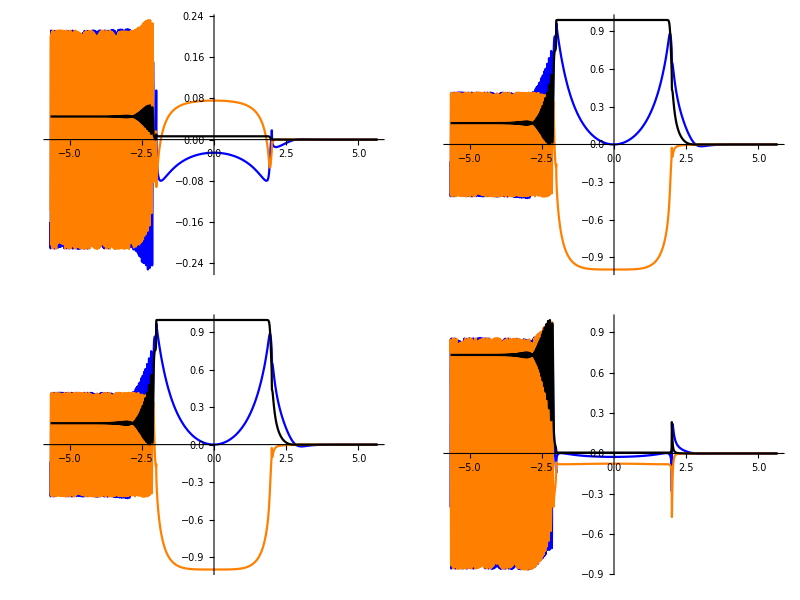
{0.784305,(-Graphics-)}

```mathematica
χ=100;υ=0.0007;θ=0;η=ArcSin[√((√υ)/(1+√υ))];
Impedance[10^-5,χ,υ,θ,η,{1,0}];
{%⟦1⟧,Table[Plot[{Re[%⟦2⟧⟦i,j⟧],Im[%⟦2⟧⟦i,j⟧],Abs[%⟦2⟧⟦i,j⟧]^2},{x,-2%⟦6⟧,2%⟦6⟧},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Orange,Black}],{i,1,2},{j,1,2}]//MatrixForm}
R=%%⟦3⟧/.x->-2%%⟦6⟧;
U=%%%⟦4⟧;
Clear[χ,υ,θ,η]
```

```mathematica
(2 √2 π (10^(3/2)(2 √2 π σ^2)^2)^(1/4) σ^2)^-1/.σ->0.08
```

31.0948